```mathematica
movies=Normal[Import["https://wolfr.am/1ijcKbZ5I","Dataset",HeaderLines->1]];
```

```mathematica
jsonStringQ[___]:=False
jsonSrtingQ[text_String]:=StringMatchQ[text,{"{","["}~~__]
```

```mathematica
jsonKeys=Keys@Select[movies[[1]],jsonSrtingQ];
```

```mathematica
fromJSON[k_String] /; MemberQ[jsonKeys, k] := ImportString[#, "RawJSON"]&
fromJSON[k_String] := Identity
fromJSON[k_, v_] := k -> fromJSON[k][v]
fromJSON[a_Association] := <|KeyValueMap[fromJSON, a]|>
```

```mathematica
movies = Map[fromJSON] @ movies; 
Dataset[movies]
```

Dataset[<>]

```mathematica
movies[[1 ;; 20 ;; 3, {"original_title", "budget", "popularity"}]] // Dataset
```

```mathematica
movies[[-1 ;;-10 ;; -2 , {"original_title", Key["budget"], "popularity"}]] // Dataset
```

```mathematica
assoc = <|All -> 1, {"one", "two"} -> {1, 2}, 
"one" -> "один", "two" -> "два", 1 -> 2, 2 -> 3, 2 ;; 3 -> 23|>;
```

```mathematica
assoc[[All]]
assoc[All]
assoc[[Key[All]]]
```

<|All→1,{one,two}→{1,2},one→один,two→два,1→2,2→3,2;;3→23|>

1

1

```mathematica
assoc[[1]]
assoc[[2]]
assoc[[{1,2}]]
assoc[[2;;3]]
```

1

{1,2}

<|All→1,{one,two}→{1,2}|>

<|{one,two}→{1,2},one→один|>

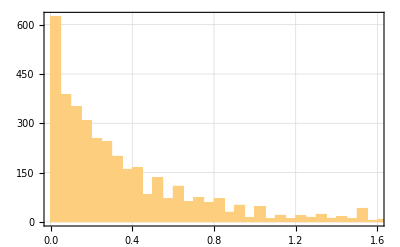

```mathematica
Histogram[Select[# > 0&] @ movies[[All,"budget"]], 
PlotTheme->"Detailed"
]
```

```mathematica
DeleteDuplicates @ Flatten @ movies[[All, "genres", All, "name"]]
```

{Action,Adventure,Fantasy,Science Fiction,Crime,Drama,Thriller,Animation,Family,Western,Comedy,Romance,Horror,Mystery,History,War,Music,Documentary,Foreign,TV Movie}

```mathematica
DeleteDuplicates @ Flatten @ movies[[All, "genres", 1;;-1, "name"]]
```

{Action,Adventure,Fantasy,Science Fiction,Crime,Drama,Thriller,Animation,Family,Western,Comedy,Romance,Horror,Mystery,History,War,Music,Documentary,Foreign,TV Movie}

```mathematica
Query[1 ;; 10, "original_title"] @ movies
```

{Avatar,Pirates of the Caribbean: At World's End,Spectre,The Dark Knight Rises,John Carter,Spider-Man 3,Tangled,Avengers: Age of Ultron,Harry Potter and the Half-Blood Prince,Batman v Superman: Dawn of Justice}

```mathematica
getGenres=Query[Flatten]@*Query[All,"genres",All,"name"]
PieChart3D[#[[2]], ChartLabels->#[[1]], ImageSize->800, LabelStyle->16]& @ 
Transpose @ 
Tally[getGenres[movies]]
```

Query[Flatten]@*Query[All,genres,All,name]

-Graphics3D-

```mathematica
Dataset[Select[#budget > 100000000&] @ movies, MaxItems->2]
```

Dataset[<>]

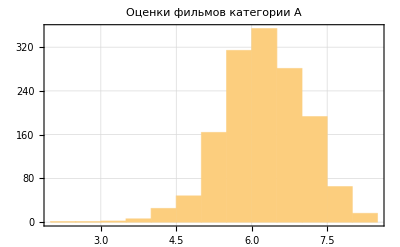

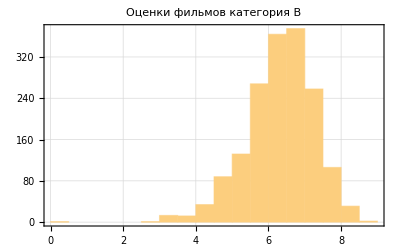

```mathematica
Histogram[Query[Select[#budget > 30000000&], "vote_average"] @ movies, 
PlotLabel -> "Оценки фильмов категории А", PlotTheme->"Detailed"]
Histogram[Query[Select[30000000 > #budget > 3000000&], "vote_average"] @ movies, 
PlotLabel->"Оценки фильмов категория B", PlotTheme->"Detailed"]
```